```mathematica
m=0.5; (*set mass in Planck units*)
tmax=40;(*set time interval in Planck units*)
tend=20;(*set time interval in Planck units*)
V[a_]:=m*m*a*a/2; (*define a quadratic potential*)
dVdx[a_]:=m*m*a;(*give the derivative of the potential*)
energy[p_,dp_]:=V[p]+(dp*dp)/2; (*the energy density*)
Hubblerate[a_,b_] := Sqrt[8*Pi*energy[a,b]/3]; (*define H *)
P[p_,dp_]:=((Hubblerate[p,dp]^2/(2*Pi*dp)^2)); (*Power spectrum*)
k[a_,p_,dp_]:=a*Hubblerate[p,dp];
w[p_,dp_]:=(-V[p]+(dp*dp)/2)/(V[p]+(dp*dp)/2); (*the equation of state*)
epsH[p_,dp_]:=(3*(dp*dp)/2)/(2*V[p]+(dp*dp)); (*the equation of state*)
xin=1; (* start by setting initial conditions for field*)
yin=0; (* initial condition for time derivative of the field*)
zin=0;(* initial condition for the N=log(scale factor)*)
(* here is where we solve 3 coupled 1st order DEs*)
nonslowroll=NDSolve[{x'[t]==y[t],y'[t]+3z'[t]*y[t]==-dVdx[x[t]],z'[t]==Sqrt[8*Pi*(V[x[t]]+y[t]*y[t]/2)/3],x[0]==xin,y[0]==yin,z[0]==zin}, {x[t],y[t],z[t]},{t,0,tmax}]; 
KGequations[pin_,dpin_]:=NDSolve[{x'[t]==y[t],y'[t]+3z'[t]*y[t]==-dVdx[x[t]],z'[t]==Sqrt[8*Pi*(V[x[t]]+y[t]*y[t]/2)/3],x[0]==pin,y[0]==dpin,z[0]==zin}, {x[t],y[t],z[t]},{t,0,tmax}];
```

Null^2

```mathematica
|
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[{Evaluate[1/2 m m x x,{x,-10,10},AxesLabel→{ϕ,V}]}]

General::prng: Value of option PlotRange -> {{t,0,40},{0,1}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

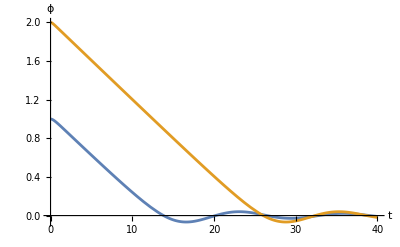

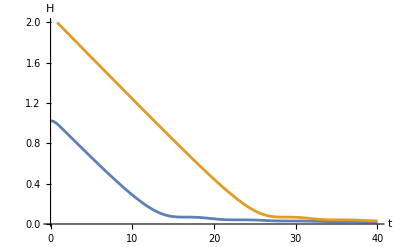

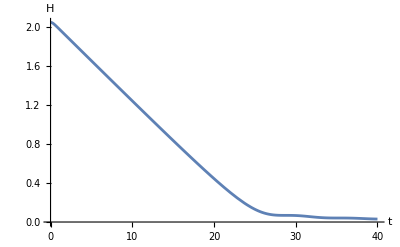

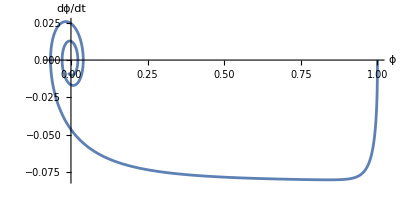

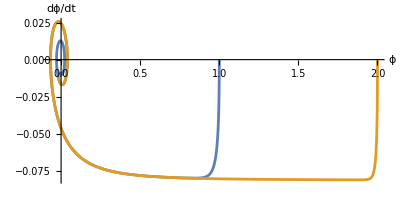

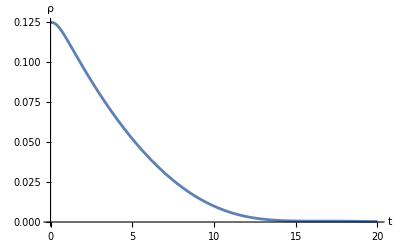

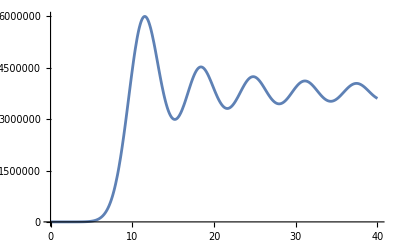

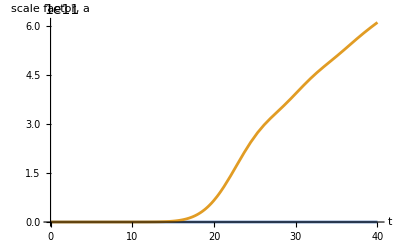

```mathematica
Plot[{Evaluate[m*m*x*x/ 2, {x,-10,10}, AxesLabel -> {ϕ, V}]}]
Plot[{Evaluate[x[t]/.KGequations[1,0]],Evaluate[x[t]/. KGequations [2,0]]},{t,0,tmax},PlotRange->{{t,0,tmax},{0,xin}},AxesLabel->{t,ϕ},LabelStyle->Directive[Blue,Medium]] (*plot field*)
Plot[{Evaluate[Hubblerate[x[t],y[t]]/.KGequations[1,0]],Evaluate[Hubblerate[x[t],y[t]]/.KGequations[2,0]]},{t,0,tmax},AxesLabel->{t,H},PlotRange->{{0,tmax},{2,0}},LabelStyle->Directive[Blue,Medium]] (*plot Hubble rate CHANGED XIN*)
Plot[{Evaluate[Hubblerate[x[t],y[t]]/.KGequations[2,0]],Evaluate[Hubblerate[x[t],y[t]/.KGequations[1,0]]]},{t,0,tmax},AxesLabel->{t,H},LabelStyle->Directive[Blue,Medium]] (*plot Hubble rate CHANGED YIN*)
ParametricPlot[{Evaluate[{x[t],y[t]}/.nonslowroll]},{t,0,tmax},AxesLabel->{ϕ,dϕ/dt},LabelStyle->Directive[Blue,Medium],AspectRatio->1/2] (*plot phi-dot vs phi*)
ParametricPlot[{Evaluate[{x[tt],y[tt]}/.{KGequations[1,0]/.t->tt}],Evaluate[{x[tt],y[tt]}/.{KGequations[2,0]/.t->tt}]},{tt,0,tmax},AxesLabel->{ϕ,dϕ/dt},LabelStyle->Directive[Blue,Medium],AspectRatio->1/2] (*plot phi-dot vs phi*)
Plot[Evaluate[energy[x[t],y[t]]/.nonslowroll],{t,0,tend},AxesLabel->{t,ρ},LabelStyle->Directive[Blue,Medium]] (*plot energy desnity*)
Plot[Evaluate[energy[x[t],y[t]]*Exp[3*z[t]]/.nonslowroll],{t,0,tmax}] (*plot TOTAL energy = energy density x scale factor^3 *)
Plot[{Evaluate[Exp[z[t]]/.KGequations[1,0]],Evaluate[Exp[z[t]]/.KGequations[2,0]]},{t,0,tmax},AxesLabel->{t,"scale factor, a"},LabelStyle->Directive[Blue,Medium]] (*plot a = e^N = scale factor *)
Plot[{Evaluate[z[t]/.KGequations[1,0]],Evaluate[z[t]/.KGequations[3,0]]},{t,0,tmax},AxesLabel->{t,N},LabelStyle->Directive[Blue,Medium]] (*plot N = log (scale factor) *)
Plot[{Evaluate[y[t]/.KGequations[1,0]],Evaluate[y[t]/.KGequations[2,0]]},{t,0,tmax},AxesLabel->{t,phi dot},LabelStyle->Directive[Blue,Medium]] (*change x*)
Plot[{Evaluate[y[t]/.KGequations[1,1]],Evaluate[y[t]/.KGequations[1,2]]},{t,0,tmax},AxesLabel->{t,phi dot},LabelStyle->Directive[Blue,Medium]] (*change y*)
Plot[{Evaluate[epsH[x[t],y[t]]/.KGequations[1,0]],Evaluate[epsH[x[t],y[t]]/.KGequations[2,0]],1},{t,0,tmax},AxesLabel->{t,ϵ},LabelStyle->Directive[Blue,Medium]] (*plot equation of state*)
Plot[Evaluate[P[x[t],y[t]]/.nonslowroll,{t,0,tend},AxesLabel->{t,P},LabelStyle->Directive[Blue,Medium]]](*plot Power spectrum*)
Plot[Evaluate[k[Exp[z[t]],x[t],y[t]]/.KGequations[xin,yin]],{t,0,tend},AxesLabel->{t,k},LabelStyle->Directive[Blue,Medium]] (*plot wavenumber k=aH*)
Plot[Evaluate[Log[k[Exp[z[t]],x[t],y[t]]/.KGequations[xin,yin]]],{t,0,tend},AxesLabel->{t,"ln(k)"},LabelStyle->Directive[Blue,Medium]] (*plot wavenumber k=aH*)
ParametricPlot[Evaluate[{Log[k[Exp[z[t]],x[t],y[t]]],Log[P[x[t],y[t]]]}/.nonslowroll],{t,0,tend},AxesLabel->{"ln(k)","ln(P)"},LabelStyle->Directive[Blue,Medium],PlotRange->{{0,4.5},{5,0}},AspectRatio->1/2] (*plot Power vs k *)
```